# Calcolo antitrasformata di Laplace per risposta forzata di un sistema LTI-TC ad un ingresso periodico elementare

Inserisco la funzione di trasferimento

```mathematica
G[s_]:=(1+2s)/((s+1)(s+3)(s+7))
```

e considero la trasformata di Laplace dell’ingresso periodico elementare

```mathematica
U[s_]:=LaplaceTransform[Sin[t] UnitStep[t],t,s]
```

```mathematica
U[s]
```

1/(1+s^2)

La risposta forzata (in s) e’ il prodotto algebrico fra la FdT e U(s)

```mathematica
Y[s_]:=G[s]U[s]
```

```mathematica
Y[s]
```

(1+2 s)/((1+s) (3+s) (7+s) (1+s^2))

```mathematica
Apart[Y[s]]
```

-1/(24 (1+s))+1/(16 (3+s))-13/(1200 (7+s))+(7-s)/(100 (1+s^2))

```mathematica
InverseLaplaceTransform[Y[s],s,t]
```

-(13 ⅇ^(-7 t))/1200+ⅇ^(-3 t)/16-ⅇ^-t/24+1/100 (-Cos[t]+7 Sin[t])

Scrivo in maniera simbolica la Y(s) mettendo in evidenza i fratti semplici (tutti, considero il trinomio non scomponibile)

```mathematica
Subscript[C, 1]/(s-ⅈ)+Subscript[C, 2]/(s+ⅈ)+Subscript[C, 3]/(s+1)+Subscript[C, 4]/(s+3)+Subscript[C, 5]/(s+7)
```

C_1/(-ⅈ+s)+C_2/(ⅈ+s)+C_3/(1+s)+C_4/(3+s)+C_5/(7+s)

Calcolo i coefficienti dei fratti semplici applicando la formula elementare di Heaviside

```mathematica
Subscript[C, 1]=lim_(s->ⅈ) (s-ⅈ)Y[s]
```

-1/200-(7 ⅈ)/200

```mathematica
Subscript[C, 2]=lim_(s->-ⅈ) (s+ⅈ)Y[s]
```

-1/200+(7 ⅈ)/200

```mathematica
Subscript[C, 3]=lim_(s->-1) (s+1)Y[s]
```

-1/24

```mathematica
Subscript[C, 4]=lim_(s->-3) (s+3)Y[s]
```

1/16

```mathematica
Subscript[C, 5]=lim_(s->-7) (s+7)Y[s]
```

-13/1200

```mathematica
Subscript[C, 1]/(s-ⅈ)+Subscript[C, 2]/(s+ⅈ)+Subscript[C, 3]/(s+1)+Subscript[C, 4]/(s+3)+Subscript[C, 5]/(s+7)
```

-(1/200+(7 ⅈ)/200)/(-ⅈ+s)-(1/200-(7 ⅈ)/200)/(ⅈ+s)-1/(24 (1+s))+1/(16 (3+s))-13/(1200 (7+s))

Mi scrivo ora la componente di regime della risposta forzata al segnale periodico elementare sin(t)

```mathematica
Subscript[y, ss][t_]:=2 ComplexExpand[Re[Subscript[C, 1] Exp[I t]]]
```

```mathematica
Subscript[y, ss][t]
```

2 (-Cos[t]/200+(7 Sin[t])/200)

```mathematica
InverseLaplaceTransform[Y[s],s,t]
```

-(13 ⅇ^(-7 t))/1200+ⅇ^(-3 t)/16-ⅇ^-t/24+1/100 (-Cos[t]+7 Sin[t])

Determino la coppia ampiezza-fase della risposta a regime . Devo quindi determinare la coppia  tale che



che si traduce in due equazioni (la prima valutando in zero il legame, la seconda valutando in zero le rispettive derivate prime)

```mathematica
Solve[{(2 (-Cos[t]/200+(7 Sin[t])/200)==X Sin[t+θ])/.{t->0},(D[2 (-Cos[t]/200+(7 Sin[t])/200),t]==D[X Sin[t+θ],t])/.{t->0},X>0},{X,θ}]
```

{{X→ConditionalExpression[1/(10 √2), C[1]∈ℤ],θ→ConditionalExpression[2 ArcTan[(-10+7 √2)/(√2)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
N[1/(10 √2)]
```

0.0707107

```mathematica
N[2 ArcTan[(-10+7 √2)/(√2)]](180/π)
```

-8.1301

Grafico della risposta forzata e della risposta a regime

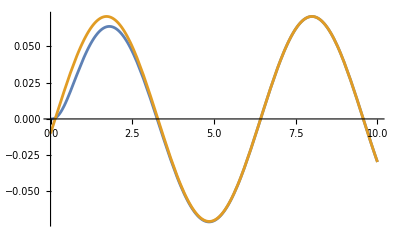

```mathematica
Plot[{-(13 ⅇ^(-7 t))/1200+ⅇ^(-3 t)/16-ⅇ^-t/24+1/100 (-Cos[t]+7 Sin[t]),2 (-Cos[t]/200+(7 Sin[t])/200)},{t,0,10},PlotRange->All]
```